```mathematica
SetDirectory["C:/Users/serha/OneDrive - Jacobs University/courses/3rd semester/Advance_Project_II/20201124_network_generation_with_Lifting/"];
```

```mathematica
data=Import["C:/Users/serha/OneDrive - Jacobs University/courses/3rd semester/Advance_Project_II/20200825_indicative_features/cgl_data_csp_sequences_only.csv",HeaderLines->1];
```

```mathematica
rawaim=data[[All,113]];
aim=DeleteCases[rawaim,"NA"];
campaign=Delete[data[[All,118]],Position[rawaim,"NA"]];
productionorder=Delete[data[[All,4]],Position[rawaim,"NA"]];
Print["unique aim data members: ",Dimensions@DeleteDuplicates@aim]
Print["aim data length: ",Dimensions@aim]
Print["amount of production order ID's: ",Dimensions@DeleteDuplicates@productionorder]
Print["amount of customer ID's: ",Dimensions@DeleteDuplicates@Delete[data[[All,6]],Position[rawaim,"NA"]]]
Print["sequence data groups amount: ",Dimensions@DeleteDuplicates@campaign]
```

unique aim data members: {906}

aim data length: {32098}

amount of production order ID's: {5873}

amount of customer ID's: {399}

sequence data groups amount: {738}

```mathematica
range=Range[500,600];
check=Table[Mod[32098,i],{i,range}]
min=Min[check]
pos=Position[Table[Mod[32098,i],{i,range}],min(*Min[Table[Mod[32098,i],{i,Range[500,600]}]]*)][[1]]
bucketsize=range[[pos]]
```

{98,34,472,409,346,283,220,157,94,31,478,416,354,292,230,168,106,44,500,439,378,317,256,195,134,73,12,478,418,358,298,238,178,118,58,533,474,415,356,297,238,179,120,61,2,488,430,372,314,256,198,140,82,24,520,463,406,349,292,235,178,121,64,7,514,458,402,346,290,234,178,122,66,10,528,473,418,363,308,253,198,143,88,33,562,508,454,400,346,292,238,184,130,76,22,563,510,457,404,351,298}

2

{45}

{544}

```mathematica
bins=Table[MinMax[i],{i,Partition[Sort[aim],bucketsize]}]
bins=Sort@Join[Drop[bins,{-1}],{{1675.27099609375,2291}}]
```

{{713.316,917.84},{917.84,1041.67},{1041.67,1127.39},{1127.39,1165.49},{1165.49,1201.39},{1201.39,1222.64},{1222.64,1222.64},{1222.64,1222.64},{1222.64,1222.64},{1222.64,1222.64},{1222.64,1222.64},{1222.64,1222.64},{1222.64,1222.64},{1222.64,1222.64},{1222.64,1222.64},{1222.64,1227.14},{1227.14,1229.04},{1229.04,1231.58},{1231.58,1231.58},{1231.58,1234.12},{1234.12,1236.66},{1236.66,1241.43},{1241.43,1247.78},{1248.35,1254.25},{1254.25,1255.71},{1255.71,1261.27},{1261.27,1264.6},{1264.6,1271.59},{1271.59,1274.76},{1274.76,1288.49},{1288.49,1320.48},{1320.48,1329.21},{1329.21,1341.44},{1341.44,1350.96},{1350.96,1373.19},{1373.19,1382.71},{1382.71,1401.76},{1401.76,1420.81},{1420.81,1427.16},{1427.16,1438.59},{1438.59,1475.68},{1475.68,1485.73},{1485.73,1497.01},{1497.01,1500.82},{1500.82,1503.36},{1503.36,1510.22},{1510.22,1526.03},{1526.03,1528.76},{1528.76,1528.76},{1528.76,1528.76},{1528.76,1528.76},{1528.76,1528.76},{1528.76,1528.76},{1528.76,1528.76},{1528.76,1529.79},{1529.79,1529.79},{1529.79,1565.64},{1565.64,1675.27},{1675.27,1847.58}}

{{713.316,917.84},{917.84,1041.67},{1041.67,1127.39},{1127.39,1165.49},{1165.49,1201.39},{1201.39,1222.64},{1222.64,1222.64},{1222.64,1222.64},{1222.64,1222.64},{1222.64,1222.64},{1222.64,1222.64},{1222.64,1222.64},{1222.64,1222.64},{1222.64,1222.64},{1222.64,1222.64},{1222.64,1227.14},{1227.14,1229.04},{1229.04,1231.58},{1231.58,1231.58},{1231.58,1234.12},{1234.12,1236.66},{1236.66,1241.43},{1241.43,1247.78},{1248.35,1254.25},{1254.25,1255.71},{1255.71,1261.27},{1261.27,1264.6},{1264.6,1271.59},{1271.59,1274.76},{1274.76,1288.49},{1288.49,1320.48},{1320.48,1329.21},{1329.21,1341.44},{1341.44,1350.96},{1350.96,1373.19},{1373.19,1382.71},{1382.71,1401.76},{1401.76,1420.81},{1420.81,1427.16},{1427.16,1438.59},{1438.59,1475.68},{1475.68,1485.73},{1485.73,1497.01},{1497.01,1500.82},{1500.82,1503.36},{1503.36,1510.22},{1510.22,1526.03},{1526.03,1528.76},{1528.76,1528.76},{1528.76,1528.76},{1528.76,1528.76},{1528.76,1528.76},{1528.76,1528.76},{1528.76,1528.76},{1528.76,1529.79},{1529.79,1529.79},{1529.79,1565.64},{1565.64,1675.27},{1675.27,2291}}

```mathematica
binning=Table[Catch[Do[If[IntervalMemberQ[Interval[i],aim[[j]]]==True,Throw[i]],
{i,bins}]],{j,Length[aim]}];
Position[binning,Null]
```

{}

```mathematica
aim=binning;
binningmembers=Sort[DeleteDuplicates[aim]]
Print["binning amount: ",Dimensions@DeleteDuplicates@binning]
Print["dimension of binned data: ",Dimensions@aim]
Print["binning members dimension : ",Dimensions@binningmembers]
```

{{713.316,917.84},{917.84,1041.67},{1041.67,1127.39},{1127.39,1165.49},{1165.49,1201.39},{1201.39,1222.64},{1222.64,1227.14},{1227.14,1229.04},{1229.04,1231.58},{1231.58,1234.12},{1234.12,1236.66},{1236.66,1241.43},{1241.43,1247.78},{1248.35,1254.25},{1254.25,1255.71},{1255.71,1261.27},{1261.27,1264.6},{1264.6,1271.59},{1271.59,1274.76},{1274.76,1288.49},{1288.49,1320.48},{1320.48,1329.21},{1329.21,1341.44},{1341.44,1350.96},{1350.96,1373.19},{1373.19,1382.71},{1382.71,1401.76},{1401.76,1420.81},{1420.81,1427.16},{1427.16,1438.59},{1438.59,1475.68},{1475.68,1485.73},{1485.73,1497.01},{1497.01,1500.82},{1500.82,1503.36},{1503.36,1510.22},{1510.22,1526.03},{1526.03,1528.76},{1528.76,1529.79},{1529.79,1565.64},{1565.64,1675.27},{1675.27,2291}}

binning amount: {42,2}

dimension of binned data: {32098,2}

binning members dimension : {42,2}

cleaning and modifying interval

```mathematica
(*part11=Take[Position[aim,{1201.39331054688,1222.64038085938}],546];*)
part12=Take[Position[aim,{1201.39331054688,1222.64038085938}],{547,1088}];
part13=Take[Position[aim,{1201.39331054688,1222.64038085938}],{1089,1630}];
part14=Take[Position[aim,{1201.39331054688,1222.64038085938}],{1631,2172}];
part15=Take[Position[aim,{1201.39331054688,1222.64038085938}],{2173,2714}];
part16=Take[Position[aim,{1201.39331054688,1222.64038085938}],{2715,3256}];
part17=Take[Position[aim,{1201.39331054688,1222.64038085938}],{3257,3798}];
part18=Take[Position[aim,{1201.39331054688,1222.64038085938}],{3799,4340}];
part19=Take[Position[aim,{1201.39331054688,1222.64038085938}],{4341,4882}];
part110=Take[Position[aim,{1201.39331054688,1222.64038085938}],{4883,5424}];
(*aim=ReplacePart[aim,part11->{"1201.39-1st","1222.64-1st"}];*)
aim=ReplacePart[aim,part12->{1201.3902,1222.6402}];
aim=ReplacePart[aim,part13->{1201.3903,1222.6403}];
aim=ReplacePart[aim,part14->{1201.3904,1222.6404}];
aim=ReplacePart[aim,part15->{1201.3905,1222.6405}];
aim=ReplacePart[aim,part16->{1201.3906,1222.6406}];
aim=ReplacePart[aim,part17->{1201.3907,1222.6407}];
aim=ReplacePart[aim,part18->{1201.3908,1222.6408}];
aim=ReplacePart[aim,part19->{1201.3909,1222.6409}];
aim=ReplacePart[aim,part110->{1201.3910,1222.6410}];

(*part21=Take[Position[aim,{1229.04248046875,1231.58251953125}],419];*)
part22=Take[Position[aim,{1229.04248046875,1231.58251953125}],{420,836}];
part23=Take[Position[aim,{1229.04248046875,1231.58251953125}],{837,1253}];
(*aim=ReplacePart[aim,part21->{"1229.04-1st","1231.58-1st"}];*)
aim=ReplacePart[aim,part22->{1229.0402,1231.5802}];
aim=ReplacePart[aim,part23->{1229.0403,1231.5803}];

(*part31=Take[Position[aim,{1526.03198242188,1528.76245117188}],539];*)
part32=Take[Position[aim,{1526.03198242188,1528.76245117188}],{540,1075}];
part33=Take[Position[aim,{1526.03198242188,1528.76245117188}],{1076,1611}];
part34=Take[Position[aim,{1526.03198242188,1528.76245117188}],{1612,2147}];
part35=Take[Position[aim,{1526.03198242188,1528.76245117188}],{2148,2683}];
part36=Take[Position[aim,{1526.03198242188,1528.76245117188}],{2684,3219}];
part37=Take[Position[aim,{1526.03198242188,1528.76245117188}],{3220,3755}];
part38=Take[Position[aim,{1526.03198242188,1528.76245117188}],{3756,4291}];
(*aim=ReplacePart[aim,part31->{"1526.03-1st","1528.76-1st"}];*)
aim=ReplacePart[aim,part32->{1526.0302,1528.7602}];
aim=ReplacePart[aim,part33->{1526.0303,1528.7603}];
aim=ReplacePart[aim,part34->{1526.0304,1528.7604}];
aim=ReplacePart[aim,part35->{1526.0305,1528.7605}];
aim=ReplacePart[aim,part36->{1526.0306,1528.7606}];
aim=ReplacePart[aim,part37->{1526.0307,1528.7607}];
aim=ReplacePart[aim,part38->{1526.0308,1528.7608}];

(*part41=Take[Position[aim,{1485.72509765625,1497.01245117188}],526];*)
part42=Take[Position[aim,{1485.72509765625,1497.01245117188}],{527,1051}];
(*aim=ReplacePart[aim,part41->{"1485.73-1st","1497.01-1st"}];*)
aim=ReplacePart[aim,part42->{1485.7302,1497.0102}];

(*part51=Take[Position[aim,{1234.12243652344,1236.66247558594}],456];*)
part52=Take[Position[aim,{1234.12243652344,1236.66247558594}],{457,912}];
(*aim=ReplacePart[aim,part51->{"1234.12-1st","1236.66-1st"}];*)
aim=ReplacePart[aim,part52->{1234.1202,1236.6602}];

(*part61=Take[Position[aim,{1264.60241699219,1271.58752441406}],438];*)
part62=Take[Position[aim,{1264.60241699219,1271.58752441406}],{439,875}];
(*aim=ReplacePart[aim,part61->{"1264.60-1st","1271.59-1st"}];*)
aim=ReplacePart[aim,part62->{1264.6002,1271.5902}];
(*join*)
part71=Take[Position[aim,{1234.12243652344,1236.66247558594}],456];
part72=Take[Position[aim,{1236.66247558594,1241.42504882812}],181];
aim=ReplacePart[aim,part71->{1234.12,1241.43}];
aim=ReplacePart[aim,part72->{1234.12,1241.43}];
(*join*)
part81=Take[Position[aim,{1497.01245117188,1500.82250976562}],151];
part82=Take[Position[aim,{1500.82250976562,1503.36242675781}],511];
aim=ReplacePart[aim,part81->{1497.01,1503.36}];
aim=ReplacePart[aim,part82->{1497.01,1503.36}];
(*join*)
part91=Take[Position[aim,{1229.04248046875,1231.58251953125}],419];
part92=Take[Position[aim,{1231.58251953125,1234.12243652344}],374];
aim=ReplacePart[aim,part91->{1229.04,1234.12}];
aim=ReplacePart[aim,part92->{1229.04,1234.12}];
```

```mathematica
binningmembers=Sort[DeleteDuplicates[aim]];
```

```mathematica
aimbaskets=Values@GroupBy[Thread[{aim,campaign}],Last->First];
aimbasketsrev=Table[DeleteDuplicates[i],{i,aimbaskets}];
productionorderbaskets=Values@GroupBy[Thread[{productionorder,aim}],Last->First];
productionorderbasketsrev=Table[DeleteDuplicates[i],{i,productionorderbaskets}];
Print["count of unique prod. order id's in each binning group: ",KeySort@Counts@Table[Length[i],{i,productionorderbasketsrev}]]
Print["binning groups association to count of unique prod. order id's: ",KeySort@MapThread[#1->#2&,{Keys@GroupBy[Thread[{productionorder,aim}],Last->First],Table[Length[i],{i,productionorderbasketsrev}]}]]
Print["binning groups association to count of their total members: ",KeySort@Counts@aim]
Print["binning amount: ",Dimensions@DeleteDuplicates@aim]
```

count of unique prod. order id's in each binning group: <|15→1,30→1,33→1,40→1,41→1,43→2,53→1,54→1,55→1,56→1,60→3,62→1,67→1,68→1,70→1,75→2,79→1,81→1,86→1,87→1,89→1,90→1,91→2,93→1,99→1,101→1,104→1,110→2,114→2,116→1,118→1,122→1,123→2,126→1,128→1,133→2,134→1,135→1,136→1,137→1,143→1,146→1,152→1,157→1,161→2,162→1,171→1,176→1,180→1,203→1|>

binning groups association to count of unique prod. order id's: <|{713.316,917.84}→171,{917.84,1041.67}→162,{1041.67,1127.39}→114,{1127.39,1165.49}→110,{1165.49,1201.39}→137,{1201.39,1222.64}→118,{1201.39,1222.64}→90,{1201.39,1222.64}→136,{1201.39,1222.64}→133,{1201.39,1222.64}→180,{1201.39,1222.64}→99,{1201.39,1222.64}→114,{1201.39,1222.64}→123,{1201.39,1222.64}→126,{1201.39,1222.64}→91,{1222.64,1227.14}→81,{1227.14,1229.04}→54,{1229.04,1234.12}→87,{1229.04,1231.58}→56,{1229.04,1231.58}→33,{1234.12,1241.43}→70,{1234.12,1236.66}→104,{1241.43,1247.78}→75,{1248.35,1254.25}→110,{1254.25,1255.71}→60,{1255.71,1261.27}→30,{1261.27,1264.6}→53,{1264.6,1271.59}→41,{1264.6,1271.59}→15,{1271.59,1274.76}→55,{1274.76,1288.49}→79,{1288.49,1320.48}→161,{1320.48,1329.21}→40,{1329.21,1341.44}→91,{1341.44,1350.96}→75,{1350.96,1373.19}→116,{1373.19,1382.71}→86,{1382.71,1401.76}→134,{1401.76,1420.81}→93,{1420.81,1427.16}→68,{1427.16,1438.59}→89,{1438.59,1475.68}→128,{1475.68,1485.73}→43,{1485.73,1497.01}→60,{1485.73,1497.01}→60,{1497.01,1503.36}→62,{1503.36,1510.22}→43,{1510.22,1526.03}→67,{1526.03,1528.76}→146,{1526.03,1528.76}→122,{1526.03,1528.76}→123,{1526.03,1528.76}→135,{1526.03,1528.76}→133,{1526.03,1528.76}→152,{1526.03,1528.76}→157,{1526.03,1528.76}→101,{1528.76,1529.79}→143,{1529.79,1565.64}→161,{1565.64,1675.27}→176,{1675.27,2291}→203|>

binning groups association to count of their total members: <|{713.316,917.84}→618,{917.84,1041.67}→492,{1041.67,1127.39}→523,{1127.39,1165.49}→557,{1165.49,1201.39}→562,{1201.39,1222.64}→542,{1201.39,1222.64}→542,{1201.39,1222.64}→542,{1201.39,1222.64}→542,{1201.39,1222.64}→542,{1201.39,1222.64}→542,{1201.39,1222.64}→542,{1201.39,1222.64}→542,{1201.39,1222.64}→542,{1201.39,1222.64}→546,{1222.64,1227.14}→572,{1227.14,1229.04}→508,{1229.04,1234.12}→793,{1229.04,1231.58}→417,{1229.04,1231.58}→417,{1234.12,1241.43}→637,{1234.12,1236.66}→456,{1241.43,1247.78}→536,{1248.35,1254.25}→562,{1254.25,1255.71}→566,{1255.71,1261.27}→763,{1261.27,1264.6}→309,{1264.6,1271.59}→437,{1264.6,1271.59}→438,{1271.59,1274.76}→431,{1274.76,1288.49}→311,{1288.49,1320.48}→556,{1320.48,1329.21}→529,{1329.21,1341.44}→576,{1341.44,1350.96}→571,{1350.96,1373.19}→709,{1373.19,1382.71}→347,{1382.71,1401.76}→738,{1401.76,1420.81}→390,{1420.81,1427.16}→506,{1427.16,1438.59}→510,{1438.59,1475.68}→798,{1475.68,1485.73}→300,{1485.73,1497.01}→526,{1485.73,1497.01}→525,{1497.01,1503.36}→662,{1503.36,1510.22}→488,{1510.22,1526.03}→525,{1526.03,1528.76}→536,{1526.03,1528.76}→536,{1526.03,1528.76}→536,{1526.03,1528.76}→536,{1526.03,1528.76}→536,{1526.03,1528.76}→536,{1526.03,1528.76}→536,{1526.03,1528.76}→539,{1528.76,1529.79}→644,{1529.79,1565.64}→525,{1565.64,1675.27}→509,{1675.27,2291}→544|>

binning amount: {60,2}

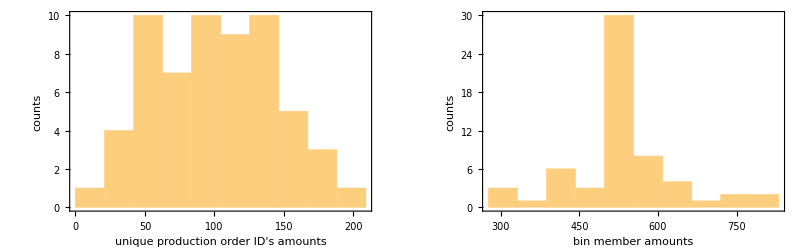

```mathematica
GraphicsRow[{Histogram[KeySort@MapThread[#1->#2&,{Keys@GroupBy[Thread[{productionorder,aim}],Last->First],Table[Length[i],{i,productionorderbasketsrev}]}],{"Raw",10},Frame->True,FrameLabel->{"unique production order ID's amounts","counts"},ImageSize->Full(*,PlotLabel->"Unique Production Order ID Counts for Each Bin"*)],Histogram[KeySort@Counts@aim,{"Raw",10},Frame->True,FrameLabel->{"bin member amounts","counts"},ImageSize->Full(*,PlotLabel->"Total Members Counts for Each Bin"*)]}]
```

```mathematica
AbsoluteTiming[singlesupportvalues=Table[N[Count[Table[MemberQ[i,j],{i,aimbasketsrev}],True]/Length[aimbasketsrev]],{j,binningmembers}];]
pairs=Subsets[binningmembers,{2}];
Dimensions[binningmembers]
Dimensions[pairs]
Dimensions[aimbasketsrev]
AbsoluteTiming[pairsupportvalues=Table[N[Count[Table[SubsetQ[i,j],{i,aimbasketsrev}],True]/
Length[aimbasketsrev]],{j,pairs}];]
```

{0.194929,Null}

{60,2}

{1770,2,2}

{738}

{15.9105,Null}

```mathematica
AbsoluteTiming[liftvalues=pairsupportvalues/(DeleteCases[Flatten@UpperTriangularize[Table[singlesupportvalues[[j]]*singlesupportvalues[[k]],{j,Length[binningmembers]},{k,Length[binningmembers]}],1],0.]);]
```

{0.0573596,Null}

```mathematica
allmatrixelements=Sort[Join[pairs,Reverse[pairs,2],Table[{i,i},{i,binningmembers}]]];
```

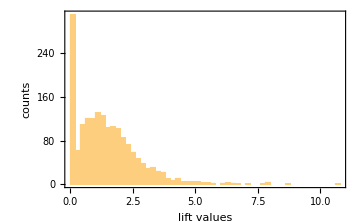

```mathematica
Histogram[liftvalues,PlotRange->All,Frame->True,FrameLabel->{"lift values","counts"},ImageSize->Medium]
```

{1047,2,2}

{0.817153,Null}

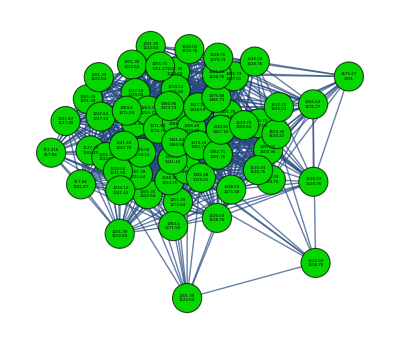

```mathematica
likelypairs=Extract[pairs,Position[liftvalues,x_/;x>1]];
Dimensions@likelypairs
AbsoluteTiming[binarymatrix=ArrayReshape[Table[If[j==True,1,0],{j,Table[MemberQ[likelypairs,i],{i,allmatrixelements}]}],{Length@binningmembers,Length@binningmembers}];]
graph=AdjacencyGraph[binarymatrix,{GraphLayout->Automatic,DirectedEdges->False,EdgeShapeFunction->"Line",VertexSize->2,VertexStyle->RGBColor[0.02,0.84,0.],VertexLabelStyle->Directive[Black,Italic,1],VertexLabels->Flatten[MapThread[{#1->Placed[#2,Center]}&,{Range[1,Dimensions[binarymatrix][[1]]],
Table[StringRiffle[i,"\n"],{i,binningmembers}]}]]},ImageSize->400]
```

Feature Projections on Width Network

Width Communities

```mathematica
com1=FindGraphCommunities[graph,Method->"Centrality"]
com2=FindGraphCommunities[graph,Method->"Modularity"]
```

{{3,4,5,8,10,11,12,13,14,16,17,18,19,20,21,22,23,24,25,26,27,28,30,31,32,33,34,35,36,37,38,39,40,41,43,45,53,54,55,57,58},{1},{2},{6},{7},{9},{15},{29},{42},{44},{46},{47},{48},{49},{50},{51},{52},{56},{59},{60}}

{{1,2,3,4,5,6,7,8,9,10,11,15,16,17,18,19,21,23,24,25,27,28,29,30,32,33,34,35,42,49,56},{22,31,37,38,39,40,41,43,44,45,46,47,48,50,51,52,53,54,55,57,58,59,60},{12,13,14,20,26,36}}

```mathematica
{a,b}={CommunityGraphPlot[graph,com1,VertexSize->1],CommunityGraphPlot[graph,com2,VertexSize->1]}
```

{-Graphics-,-Graphics-}

```mathematica
foundCommunities=com2;
communityColors=GraphComputation`GraphInformationDump`$AutomaticColorList;
Table[Thread[foundCommunities[[i]]->communityColors[[i]]],{i,1,Length@foundCommunities}]
```

{{1→Hue[0, 1, 0.8],2→Hue[0, 1, 0.8],3→Hue[0, 1, 0.8],4→Hue[0, 1, 0.8],5→Hue[0, 1, 0.8],6→Hue[0, 1, 0.8],7→Hue[0, 1, 0.8],8→Hue[0, 1, 0.8],9→Hue[0, 1, 0.8],10→Hue[0, 1, 0.8],11→Hue[0, 1, 0.8],15→Hue[0, 1, 0.8],16→Hue[0, 1, 0.8],17→Hue[0, 1, 0.8],18→Hue[0, 1, 0.8],19→Hue[0, 1, 0.8],21→Hue[0, 1, 0.8],23→Hue[0, 1, 0.8],24→Hue[0, 1, 0.8],25→Hue[0, 1, 0.8],27→Hue[0, 1, 0.8],28→Hue[0, 1, 0.8],29→Hue[0, 1, 0.8],30→Hue[0, 1, 0.8],32→Hue[0, 1, 0.8],33→Hue[0, 1, 0.8],34→Hue[0, 1, 0.8],35→Hue[0, 1, 0.8],42→Hue[0, 1, 0.8],49→Hue[0, 1, 0.8],56→Hue[0, 1, 0.8]},{22→Hue[0.14, 1, 0.9],31→Hue[0.14, 1, 0.9],37→Hue[0.14, 1, 0.9],38→Hue[0.14, 1, 0.9],39→Hue[0.14, 1, 0.9],40→Hue[0.14, 1, 0.9],41→Hue[0.14, 1, 0.9],43→Hue[0.14, 1, 0.9],44→Hue[0.14, 1, 0.9],45→Hue[0.14, 1, 0.9],46→Hue[0.14, 1, 0.9],47→Hue[0.14, 1, 0.9],48→Hue[0.14, 1, 0.9],50→Hue[0.14, 1, 0.9],51→Hue[0.14, 1, 0.9],52→Hue[0.14, 1, 0.9],53→Hue[0.14, 1, 0.9],54→Hue[0.14, 1, 0.9],55→Hue[0.14, 1, 0.9],57→Hue[0.14, 1, 0.9],58→Hue[0.14, 1, 0.9],59→Hue[0.14, 1, 0.9],60→Hue[0.14, 1, 0.9]},{12→Hue[0.8, 0.6, 0.8],13→Hue[0.8, 0.6, 0.8],14→Hue[0.8, 0.6, 0.8],20→Hue[0.8, 0.6, 0.8],26→Hue[0.8, 0.6, 0.8],36→Hue[0.8, 0.6, 0.8]}}

Thickness Communities Projection

```mathematica
projecteddata=Import["projection_data_thickness_bucket_544_60.csv"];
projecteddatauniquemembers=Sort@DeleteCases[DeleteDuplicates@projecteddata,"NA"];
```

```mathematica
nolinkcolor=Hue[0,0,0];
thicknesscommunities1={{1->Hue[0, 1, 0.8],2->Hue[0, 1, 0.8],3->Hue[0, 1, 0.8],4->Hue[0, 1, 0.8],5->Hue[0, 1, 0.8],6->Hue[0, 1, 0.8],10->Hue[0, 1, 0.8],11->Hue[0, 1, 0.8],12->Hue[0, 1, 0.8],15->Hue[0, 1, 0.8],16->Hue[0, 1, 0.8],19->Hue[0, 1, 0.8]},{37->Hue[0.14, 1, 0.9],39->Hue[0.14, 1, 0.9],40->Hue[0.14, 1, 0.9],47->Hue[0.14, 1, 0.9],48->Hue[0.14, 1, 0.9],49->Hue[0.14, 1, 0.9],55->Hue[0.14, 1, 0.9]},{52->Hue[0.8, 0.6, 0.8],53->Hue[0.8, 0.6, 0.8],54->Hue[0.8, 0.6, 0.8],56->Hue[0.8, 0.6, 0.8],57->Hue[0.8, 0.6, 0.8],58->Hue[0.8, 0.6, 0.8],59->Hue[0.8, 0.6, 0.8]},{7->Hue[0.07, 1, 1],8->Hue[0.07, 1, 1],9->Hue[0.07, 1, 1],17->Hue[0.07, 1, 1],31->Hue[0.07, 1, 1],32->Hue[0.07, 1, 1]},{18->Hue[0.2, 1, 0.6],23->Hue[0.2, 1, 0.6],27->Hue[0.2, 1, 0.6],30->Hue[0.2, 1, 0.6],34->Hue[0.2, 1, 0.6],60->Hue[0.2, 1, 0.6]},{13->Hue[0.1, 0.6, 0.7]},{14->Hue[0.5, 1, 0.7]},{20->nolinkcolor},{21->nolinkcolor},{22->nolinkcolor},{24->nolinkcolor},{25->nolinkcolor},{26->nolinkcolor},{28->nolinkcolor},{29->nolinkcolor},{33->nolinkcolor},{35->nolinkcolor},{36->nolinkcolor},{38->nolinkcolor},{41->nolinkcolor},{42->nolinkcolor},{43->nolinkcolor},{44->nolinkcolor},{45->nolinkcolor},{46->nolinkcolor},{50->nolinkcolor},{51->nolinkcolor}};
thicknesscommunities2={{1->Hue[0, 1, 0.8],2->Hue[0, 1, 0.8],5->Hue[0, 1, 0.8],10->Hue[0, 1, 0.8],11->Hue[0, 1, 0.8],15->Hue[0, 1, 0.8],16->Hue[0, 1, 0.8],18->Hue[0, 1, 0.8],23->Hue[0, 1, 0.8],27->Hue[0, 1, 0.8],30->Hue[0, 1, 0.8],34->Hue[0, 1, 0.8],60->Hue[0, 1, 0.8]},{3->Hue[0.14, 1, 0.9],4->Hue[0.14, 1, 0.9],6->Hue[0.14, 1, 0.9],7->Hue[0.14, 1, 0.9],8->Hue[0.14, 1, 0.9],9->Hue[0.14, 1, 0.9],12->Hue[0.14, 1, 0.9],17->Hue[0.14, 1, 0.9],19->Hue[0.14, 1, 0.9],31->Hue[0.14, 1, 0.9],32->Hue[0.14, 1, 0.9]},{52->Hue[0.8, 0.6, 0.8],53->Hue[0.8, 0.6, 0.8],54->Hue[0.8, 0.6, 0.8],55->Hue[0.8, 0.6, 0.8],56->Hue[0.8, 0.6, 0.8],57->Hue[0.8, 0.6, 0.8],58->Hue[0.8, 0.6, 0.8],59->Hue[0.8, 0.6, 0.8]},{37->Hue[0.07, 1, 1],39->Hue[0.07, 1, 1],40->Hue[0.07, 1, 1],47->Hue[0.07, 1, 1],48->Hue[0.07, 1, 1],49->Hue[0.07, 1, 1]},{13->Hue[0.2, 1, 0.6]},{14->Hue[0.1, 0.6, 0.7]},{20->Hue[0.5, 1, 0.7]},{21->nolinkcolor},{22->nolinkcolor},{24->nolinkcolor},{25->nolinkcolor},{26->nolinkcolor},{28->nolinkcolor},{29->nolinkcolor},{33->nolinkcolor},{35->nolinkcolor},{36->nolinkcolor},{38->nolinkcolor},{41->nolinkcolor},{42->nolinkcolor},{43->nolinkcolor},{44->nolinkcolor},{45->nolinkcolor},{46->nolinkcolor},{50->nolinkcolor},{51->nolinkcolor}};
communities=thicknesscommunities1;
```

```mathematica
associatedintervals=MapThread[#1->#2&,{projecteddatauniquemembers,Sort@Flatten@Keys@communities}];
```

```mathematica
associatedcolors=Join[associatedintervals/.Flatten@communities,{0->RGBColor[0.9,0.9,0.9]}];
```

```mathematica
majorityfornodes=Flatten[Table[Commonest[i,1],{i,Values[Normal@KeySort[GroupBy[MapThread[#1->#2&,{aim,projecteddata}],First->Last]]]}]];
elementsforvoting=Values[Normal@KeySort[GroupBy[MapThread[#1->#2&,{aim,projecteddata}],First->Last]]];
votes=Table[Tally[elementsforvoting[[i]]],{i,Length[elementsforvoting]}];
voteswithmorethanhalf=Table[If[Flatten[votes[[j]][[Flatten@Position[votes[[j]][[All,2]],Max@votes[[j]][[All,2]]]]]][[2]]>0.5*Length[elementsforvoting[[j]]],Flatten[votes[[j]][[Flatten@Position[votes[[j]][[All,2]],Max@votes[[j]][[All,2]]]]]],{0,0}],{j,Length[elementsforvoting]}];
colorsprojecteddataonnetworknodes=voteswithmorethanhalf[[All,1]]/.associatedcolors;
```

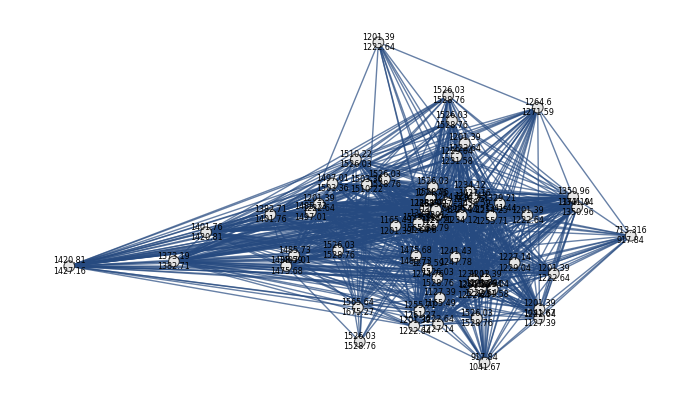

```mathematica
projectedgraph=AdjacencyGraph[binarymatrix,{GraphLayout->"SpringEmbedding",DirectedEdges->False,EdgeShapeFunction->"Line",VertexSize->2,VertexStyle->MapThread[#1->#2&,{Range[1,Dimensions[binarymatrix][[1]]],colorsprojecteddataonnetworknodes}],VertexLabelStyle->Directive[Black,Italic,8],VertexLabels->Flatten[MapThread[{#1->Placed[#2,Center]}&,{Range[1,Dimensions[binarymatrix][[1]]],
Table[StringRiffle[i,"\n"],{i,binningmembers}]}]]},ImageSize->700]
```

Steel Grade Communities Projection

```mathematica
projection=data[[All,34]];
projecteddata=Delete[projection,Position[rawaim,"NA"]];
projecteddatauniquemembers=Sort@DeleteCases[DeleteDuplicates@projection,"NA"];
```

```mathematica
steelgradecommunities1={{1->Hue[0, 1, 0.8],5->Hue[0, 1, 0.8],6->Hue[0, 1, 0.8],8->Hue[0, 1, 0.8],9->Hue[0, 1, 0.8],10->Hue[0, 1, 0.8],11->Hue[0, 1, 0.8],13->Hue[0, 1, 0.8],14->Hue[0, 1, 0.8],18->Hue[0, 1, 0.8]},{3->Hue[0.14, 1, 0.9],4->Hue[0.14, 1, 0.9],12->Hue[0.14, 1, 0.9]},{15->Hue[0.8, 0.6, 0.8],17->Hue[0.8, 0.6, 0.8]},{2->Hue[0.07, 1, 1]},{7->Hue[0.2, 1, 0.6]},{16->Hue[0.1, 0.6, 0.7]},{19->Hue[0.5, 1, 0.7]}};
steelgradecommunities2={{1->Hue[0, 1, 0.8],2->Hue[0, 1, 0.8],8->Hue[0, 1, 0.8],9->Hue[0, 1, 0.8],15->Hue[0, 1, 0.8],16->Hue[0, 1, 0.8],17->Hue[0, 1, 0.8],18->Hue[0, 1, 0.8],19->Hue[0, 1, 0.8]},{5->Hue[0.14, 1, 0.9],6->Hue[0.14, 1, 0.9],10->Hue[0.14, 1, 0.9],11->Hue[0.14, 1, 0.9],13->Hue[0.14, 1, 0.9],14->Hue[0.14, 1, 0.9]},{3->Hue[0.8, 0.6, 0.8],4->Hue[0.8, 0.6, 0.8],12->Hue[0.8, 0.6, 0.8]},{7->Hue[0.07, 1, 1]}};
```

```mathematica
associatedcolors=Join[Flatten[steelgradecommunities2/.MapThread[#1->#2&,{Range[Length[projecteddatauniquemembers]],projecteddatauniquemembers}]],{0->RGBColor[0.9,0.9,0.9]}]
```

{26→Hue[0, 26, 0.8],27→Hue[0, 26, 0.8],38→Hue[0, 26, 0.8],39→Hue[0, 26, 0.8],72→Hue[0, 26, 0.8],81→Hue[0, 26, 0.8],91→Hue[0, 26, 0.8],100→Hue[0, 26, 0.8],103→Hue[0, 26, 0.8],33→Hue[0.14, 26, 0.9],34→Hue[0.14, 26, 0.9],41→Hue[0.14, 26, 0.9],48→Hue[0.14, 26, 0.9],55→Hue[0.14, 26, 0.9],61→Hue[0.14, 26, 0.9],30→Hue[0.8, 0.6, 0.8],31→Hue[0.8, 0.6, 0.8],49→Hue[0.8, 0.6, 0.8],35→Hue[0.07, 26, 26],0→RGBColor[0.9, 0.9, 0.9]}

```mathematica
majorityfornodes=Flatten[Table[Commonest[i,1],{i,Values[Normal@KeySort[GroupBy[MapThread[#1->#2&,{aim,projecteddata}],First->Last]]]}]];
elementsforvoting=Values[Normal@KeySort[GroupBy[MapThread[#1->#2&,{aim,projecteddata}],First->Last]]];
votes=Table[Tally[elementsforvoting[[i]]],{i,Length[elementsforvoting]}];
voteswithmorethanhalf=Table[If[Flatten[votes[[j]][[Flatten@Position[votes[[j]][[All,2]],Max@votes[[j]][[All,2]]]]]][[2]]>0.5*Length[elementsforvoting[[j]]],Flatten[votes[[j]][[Flatten@Position[votes[[j]][[All,2]],Max@votes[[j]][[All,2]]]]]],{0,0}],{j,Length[elementsforvoting]}];
colorsprojecteddataonnetworknodes=voteswithmorethanhalf[[All,1]]/.associatedcolors;
```

```mathematica
voteswithmorethanhalf
votes[[{7,9,24,44,49,52,57,58,59}]]
```

{{26,560},{26,334},{26,375},{0,0},{0,0},{26,428},{26,416},{26,439},{26,315},{26,463},{26,390},{26,366},{26,358},{26,508},{26,539},{0,0},{26,351},{26,543},{26,245},{26,244},{0,0},{26,292},{31,273},{26,356},{26,465},{31,637},{0,0},{26,393},{41,273},{38,221},{26,219},{26,340},{26,497},{26,431},{0,0},{26,373},{31,178},{26,407},{26,286},{26,411},{31,379},{26,520},{31,170},{26,308},{0,0},{26,404},{38,284},{26,390},{26,418},{26,371},{26,295},{26,411},{26,329},{26,371},{26,291},{26,413},{26,613},{26,294},{26,362},{26,290}}

{{{26,416},{38,4},{30,62},{31,60}},{{26,315},{31,41},{30,183},{38,2},{61,1}},{{26,356},{61,1},{31,95},{38,94},{39,4},{41,11},{NA,1}},{{41,2},{26,308},{31,204},{38,5},{30,7}},{{30,28},{26,418},{31,69},{38,21}},{{26,411},{38,68},{31,27},{30,28},{39,2}},{{38,20},{26,613},{NA,11}},{{26,294},{31,107},{39,18},{38,101},{41,2},{NA,3}},{{26,362},{30,44},{38,21},{31,13},{41,3},{39,62},{NA,4}}}

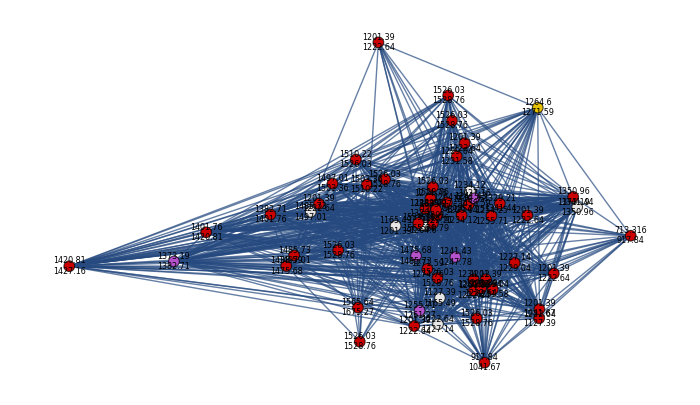

```mathematica
projectedgraph=AdjacencyGraph[binarymatrix,{GraphLayout->"SpringEmbedding",DirectedEdges->False,EdgeShapeFunction->"Line",VertexSize->2,VertexStyle->MapThread[#1->#2&,{Range[1,Dimensions[binarymatrix][[1]]],colorsprojecteddataonnetworknodes}],VertexLabelStyle->Directive[Black,Italic,8],VertexLabels->Flatten[MapThread[{#1->Placed[#2,Center]}&,{Range[1,Dimensions[binarymatrix][[1]]],
Table[StringRiffle[i,"\n"],{i,binningmembers}]}]]},ImageSize->700]
```